## Generalized Cylindrical Coordinates Transformation

Forward Transformation

```mathematica
x1[t_]=2 R[t] Cos[θ[t]]+Z[t];
x2[t_]=-R[t]Cos[θ[t]]-√3 R[t]Sin[θ[t]]+Z[t];
x3[t_]=-R[t]Cos[θ[t]]+√3 R[t]Sin[θ[t]]+Z[t];

deriv1[R_,θ_,Z_]=D[x1[t],t]
deriv2[R_,θ_,Z_]=D[x2[t],t]
deriv3[R_,θ_,Z_]=D[x3[t],t]
```

2 Cos[θ[t]] R'[t]+Z'[t]-2 R[t] Sin[θ[t]] θ'[t]

-Cos[θ[t]] R'[t]-√3 Sin[θ[t]] R'[t]+Z'[t]-√3 Cos[θ[t]] R[t] θ'[t]+R[t] Sin[θ[t]] θ'[t]

-Cos[θ[t]] R'[t]+√3 Sin[θ[t]] R'[t]+Z'[t]+√3 Cos[θ[t]] R[t] θ'[t]+R[t] Sin[θ[t]] θ'[t]

Inverse Transformation

```mathematica
Rtransform[N1_,N2_,N3_]=1/(3 √2)(√((N1-N2)^2+(N2-N3)^2+(N3-N1)^2));
θtransform[N1_,N2_,N3_]=(√3(N3-N2))/(2N1-N2-N3);
Ztransform[N1_,N2_,N3_]=((N1+N2+N3)+2λ-1)/3;
```

## May-Leonard equations

Right Hand Side

```mathematica
f1[N1_,N2_,N3_]=N1(1-N1-α N2-β N3);
f2[N1_,N2_,N3_]=N2(1-β N1-N2-α N3);
f3[N1_,N2_,N3_]=N3(1-α N1-β N2-N3);
xstar=1/(1+α+β);
```

### Transformation to Cylindrical Coordinates

```mathematica
(*transformation to cylindrical coordinates with parameters α,β*)
MLtransform=Simplify[Solve[{deriv1[R,θ,Z]==f1[x1[t]+xstar,x2[t]+xstar,x3[t]+xstar],deriv2[R,θ,Z]==f2[x1[t]+xstar,x2[t]+xstar,x3[t]+xstar],deriv3[R,θ,Z]==f3[x1[t]+xstar,x2[t]+xstar,x3[t]+xstar]},{R'[t],θ'[t],Z'[t]}]];
%/.{(4+α^2+5 β+β^2+α (5+2 β))->σ^2+3σ};

(*transformation to cylindrical coordinates with parameters λ,σ,ω*)
MLnewcoord=Simplify[%/.{(α+β+1)->σ,(α+β-2)->2λ σ,(α-β)->-2/(√3)ω σ}]
```

{{R'[t]→1/2 R[t] (2 λ+2 σ R[t] (λ Cos[3 θ[t]]-ω Sin[3 θ[t]])-(3+σ) Z[t]),θ'[t]→ω-σ R[t] (ω Cos[3 θ[t]]+λ Sin[3 θ[t]])+σ ω Z[t],Z'[t]→2 λ σ R[t]^2-Z[t] (1+σ Z[t])}}

```mathematica
(*Note: this is to check that we can replace (4+α^2+5 β+β^2+α (5+2 β))=(α+β+1)^2+3(α+β+1)->σ^2+3σ *)
Expand[(4+α^2+5 β+β^2+α (5+2 β))]==Expand[(α+β+1)^2+3(α+β+1)]
```

True

### Equations in Cylindrical Coordinates

```mathematica
(*equations in cylindrical coordinates with parameters λ,σ,ω*)
ff1[R_,θ_,Z_]=MLnewcoord[[1,1,2]]/.{R[t]->R,θ[t]->θ,Z[t]->Z};
ff2[R_,θ_,Z_]=MLnewcoord[[1,2,2]]/.{R[t]->R,θ[t]->θ,Z[t]->Z};
ff3[R_,θ_,Z_]=MLnewcoord[[1,3,2]]/.{R[t]->R,θ[t]->θ,Z[t]->Z};

(*equations in cylindrical coordinates with parameters α,β*)
ff1ab[R_,θ_,Z_]=MLtransform[[1,1,2]]/.{R[t]->R,θ[t]->θ,Z[t]->Z}
ff2ab[R_,θ_,Z_]=MLtransform[[1,2,2]]/.{R[t]->R,θ[t]->θ,Z[t]->Z}
ff3ab[R_,θ_,Z_]=MLtransform[[1,3,2]]/.{R[t]->R,θ[t]->θ,Z[t]->Z}
```

1/6 R ((3 (-2+α+β-Z (4+α^2+5 β+β^2+α (5+2 β))))/(1+α+β)+3 R ((-2+α+β) Cos[3 θ]+√3 (α-β) Sin[3 θ]))

(-3 (α-β) (1+Z (1+α+β))-R (1+α+β) (-3 (α-β) Cos[3 θ]+√3 (-2+α+β) Sin[3 θ]))/(2 √3 (1+α+β))

R^2 (-2+α+β)-Z (1+Z (1+α+β))

## May-Leonard with linear perturbation

Right Hand Side

```mathematica
g1[N1_,N2_,N3_]=N1(1-N1-α N2-β N3)+μ(-2N1+N2+N3);
g2[N1_,N2_,N3_]=N2(1-β N1-N2-α N3)+μ(N1-2N2+N3);
g3[N1_,N2_,N3_]=N3(1-α N1-β N2-N3)+μ(N1+N2-2N3);
xstar=1/(1+α+β);
```

### Transformation to Cylindrical Coordinates

```mathematica
(*using same parameter conversion as regular ML*)

(*transformation to cylindrical coordinates with parameters α,β*)
transformMLperturb=Simplify[Solve[{deriv1[R,θ,Z]==g1[x1[t]+xstar,x2[t]+xstar,x3[t]+xstar],deriv2[R,θ,Z]==g2[x1[t]+xstar,x2[t]+xstar,x3[t]+xstar],deriv3[R,θ,Z]==g3[x1[t]+xstar,x2[t]+xstar,x3[t]+xstar]},{R'[t],θ'[t],Z'[t]}]]

(*transformation to cylindrical coordinates with parameters λ,σ,ω*)
%/.{(4+α^2+5 β+β^2+α (5+2 β))->σ^2+3σ};
FullSimplify[%/.{(α+β+1)->σ,(α+β-2)->2λ σ,(α-β)->-2/(√3)ω σ}];
RHSnewcoord=Simplify[%/.{(α+β+1)->σ,(α+β-2)->2λ σ,(α-β)->-2/(√3)ω σ}]
```

{{R'[t]→1/6 R[t] (3 R[t] ((-2+α+β) Cos[3 θ[t]]+√3 (α-β) Sin[3 θ[t]])+(3 (-2+α+β-6 μ-6 α μ-6 β μ-(4+α^2+5 β+β^2+α (5+2 β)) Z[t]))/(1+α+β)),θ'[t]→((1+α+β) R[t] (-3 (-1+β) Cos[2 θ[t]]+3 (-1+α) Cos[4 θ[t]]+√3 (1-2 α+β+2 (1+α-2 β) Cos[2 θ[t]]) Sin[2 θ[t]])-3 (α-β) (Cos[θ[t]]+√3 Sin[θ[t]]) (1+(1+α+β) Z[t]))/(2 (1+α+β) (√3 Cos[θ[t]]+3 Sin[θ[t]])),Z'[t]→(-2+α+β) R[t]^2-Z[t] (1+(1+α+β) Z[t])}}

{{R'[t]→1/2 R[t] (2 λ-6 μ+2 σ R[t] (λ Cos[3 θ[t]]-ω Sin[3 θ[t]])-(3+σ) Z[t]),θ'[t]→ω-σ R[t] (ω Cos[3 θ[t]]+λ Sin[3 θ[t]])+σ ω Z[t],Z'[t]→2 λ σ R[t]^2-Z[t] (1+σ Z[t])}}

### Equations in Cylindrical Coordinates

```mathematica
(*equations in cylindrical coordinates with parameters λ,σ,ω*)
gg1[R_,θ_,Z_]=RHSnewcoord[[1,1,2]]/.{R[t]->R,θ[t]->θ,Z[t]->Z};
gg2[R_,θ_,Z_]=RHSnewcoord[[1,2,2]]/.{R[t]->R,θ[t]->θ,Z[t]->Z};
gg3[R_,θ_,Z_]=RHSnewcoord[[1,3,2]]/.{R[t]->R,θ[t]->θ,Z[t]->Z};

(*equations in cylindrical coordinates with parameters α,β*)
gg1ab[R_,θ_,Z_]=transformMLperturb[[1,1,2]]/.{R[t]->R,θ[t]->θ,Z[t]->Z};
gg2ab[R_,θ_,Z_]=transformMLperturb[[1,2,2]]/.{R[t]->R,θ[t]->θ,Z[t]->Z};
gg3ab[R_,θ_,Z_]=transformMLperturb[[1,3,2]]/.{R[t]->R,θ[t]->θ,Z[t]->Z};
```

### Solve for Fixed Points Numerically

```mathematica
α=1.1;β=1.1;μ=0.01;
(α+β-2)/(6(1+α+β))
NSolve[{gg1ab[R,θ,Z]==0,gg2ab[R,θ,Z]==0,gg3ab[R,θ,Z]==0},{R,θ,Z}]
Clear[α,β,μ]
```

0.0104167

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

NSolve::svars: Equations may not give solutions for all "solve" variables.

{{R→-0.0116575,θ→-2.0944,Z→0.0000271771},{R→-0.0116575,θ→0.,Z→0.0000271771},{R→-0.0116575,θ→2.0944,Z→0.0000271771},{R→0.0116575,θ→-3.14159,Z→0.0000271771},{R→0.0116575,θ→-1.0472,Z→0.0000271771},{R→0.0116575,θ→1.0472,Z→0.0000271771},{R→0.0116575,θ→3.14159,Z→0.0000271771},{R→-0.176102,θ→-3.14159,Z→0.00608393},{R→-0.176102,θ→-1.0472,Z→0.00608393},{R→-0.176102,θ→1.0472,Z→0.00608393},{R→-0.176102,θ→3.14159,Z→0.00608393},{R→0.176102,θ→-2.0944,Z→0.00608393},{R→0.176102,θ→0.,Z→0.00608393},{R→0.176102,θ→2.0944,Z→0.00608393}}

### Derive and Check the Fixed Points

```mathematica
(*check that these two expressions are equal*)
(*so that we can use ff2ab below instead of gg2ab -- the format of ff2ab is much nicer than gg2ab*)
Simplify[ff2ab[R,θ,Z]-gg2ab[R,θ,Z]]
```

0

#### when λ≠0, need ω=0 to find a fixed point (i.e. this means α=β) μ also needs to equal something special (have: (R,θ,Z) = (1/3-μ/λ, (2 π n)/3, 2λ R^*) but only when μ = 0,λ/3 ----> which is just R=0)

```mathematica
(*assuming that θ=0 *)
gg3[R,0,Z]
gg2[R,0,Z]/.{(ω+Z σ ω)->(2 R^2 λ σ ω)/Z}
Solve[%==0,Z]
Zwhentheta0=%[[1,1,2]];

Solve[gg1[R,0,2 R λ]==0,R]
Rwhentheta0=%[[2,1,2]];

Solve[(gg3[Rwhentheta0,0,Zwhentheta0]/.{R->Rwhentheta0})==0,μ]
%/.{σ->1+α+β,λ->(α+β-2)/(2(1+α+β))}
```

2 R^2 λ σ-Z (1+Z σ)

-R σ ω+(2 R^2 λ σ ω)/Z

{{Z→2 R λ}}

{{R→0},{R→(λ-3 μ)/(3 λ)}}

{{μ→λ/3},{μ→(λ (3-σ+2 λ σ))/(3 (-1+2 λ) σ)}}

{{μ→(-2+α+β)/(6 (1+α+β))},{μ→0}}

```mathematica
Simplify[gg1[Rwhentheta0,0,Zwhentheta0/.{R->Rwhentheta0}]]
FullSimplify[gg2[Rwhentheta0,0,Zwhentheta0/.{R->Rwhentheta0}]/.{μ->λ/3}]
FullSimplify[gg3[Rwhentheta0,0,Zwhentheta0/.{R->Rwhentheta0}]/.{μ->λ/3}]
```

0

ω

0

#### calculate fixed points with parameters (α,β)

```mathematica
(*solve 3rd eqn for (1+Z (1+α+β))*)
gg3ab[R,θ,Z]

(*substitute into 2nd eqn and solve for Z*)
Simplify[ff2ab[R,θ,Z]/.{(1+Z (1+α+β))->(R^2(-2+α+β))/Z}](2 √3(1+α+β))/R
Simplify[Solve[%==0,Z]]
Zsolve=%[[1,1,2]];

(*substitute into 1st eqn and solve for R*)
Collect[Simplify[Expand[(gg1ab[R,θ,Z] 6/R)/.{Z->Zsolve}]]((1+α+β) (-3 (α-β) Cos[3 θ]+√3 (-2+α+β) Sin[3 θ])),R]
Simplify[Solve[%==0,R]]
Rsolve=%[[1,1,2]];

(*substitute R, Z into 3rd equation to solve for θ*)
FullSimplify[gg3ab[Rsolve,θ,Zsolve/.{R->Rsolve}]]
Collect[Numerator[%]/.{Cos[6θ]-> Cos[3θ]^2-Sin[3θ]^2,Sin[6θ]->2 Sin[3θ] Cos[3θ]}/.{(3 (-α+β) Cos[3 θ]+√3 (-2+α+β) Sin[3 θ])^2->(9 (-α+β)^2 Cos[3 θ]^2+6 √3(-α+β)(-2+α+β)Cos[3θ]Sin[3θ]+3 (-2+α+β)^2 Sin[3 θ]^2)},Sin[3θ]]

(*notice that if we get rid of the Sin[3θ], we are still stuck with a term that depends just on the parameters (there's a Cos[3θ] in there too), and if we can't set that part to 0, we are out of luck with finding a fixed point*)
Simplify[%/.{θ->0}]
Solve[%==0,μ]
```

R^2 (-2+α+β)-Z (1+Z (1+α+β))

-(3 R (α-β) (-2+α+β))/Z-(1+α+β) (-3 (α-β) Cos[3 θ]+√3 (-2+α+β) Sin[3 θ])

{{Z→-(3 R (-2 α+α^2-(-2+β) β))/((1+α+β) (-3 (α-β) Cos[3 θ]+√3 (-2+α+β) Sin[3 θ]))}}

-3 (-3 (α-β) (2-β+6 μ+6 β μ+α (-1+6 μ)) Cos[3 θ]-4 √3 Sin[3 θ]+4 √3 α Sin[3 θ]-√3 α^2 Sin[3 θ]+4 √3 β Sin[3 θ]-2 √3 α β Sin[3 θ]-√3 β^2 Sin[3 θ]-12 √3 μ Sin[3 θ]-6 √3 α μ Sin[3 θ]+6 √3 α^2 μ Sin[3 θ]-6 √3 β μ Sin[3 θ]+12 √3 α β μ Sin[3 θ]+6 √3 β^2 μ Sin[3 θ])-3 R (24 α-6 α^2-3 α^3-24 β-3 α^2 β+6 β^2+3 α β^2+3 β^3+3 (α^3+α^2 (-1+β)+β (2+β-β^2)-α (2+β^2)) Cos[6 θ]-2 √3 Sin[6 θ]+3 √3 α^2 Sin[6 θ]+√3 α^3 Sin[6 θ]-3 √3 α^2 β Sin[6 θ]+3 √3 β^2 Sin[6 θ]-3 √3 α β^2 Sin[6 θ]+√3 β^3 Sin[6 θ])

{{R→-(((2+6 μ+α (-1+6 μ)+β (-1+6 μ)) (-3 (α-β) Cos[3 θ]+√3 (-2+α+β) Sin[3 θ]))/(-3 (α^3+α^2 (2+β)-α (8+β^2)-β (-8+2 β+β^2))+3 (α^3+α^2 (-1+β)+β (2+β-β^2)-α (2+β^2)) Cos[6 θ]+√3 (-2+α^3-3 α^2 (-1+β)+3 β^2-3 α β^2+β^3) Sin[6 θ]))}}

((2-α-β+6 (1+α+β) μ) (-(2-α-β) (2-α-β+6 (1+α+β) μ) (3 (-α+β) Cos[3 θ]+√3 (-2+α+β) Sin[3 θ])^2-3 (α-β) (-2+α+β) (6 (α-β) (-2+α+β) (-1+3 μ)+3 (α-β) (-2+α+β) Cos[6 θ]+√3 (-2+α^2+α (2-4 β)+β (2+β)) Sin[6 θ])))/(-3 (α-β) (-2+α+β) (4+α+β)+3 (α-β) (-2+α+β) (1+α+β) Cos[6 θ]+√3 (1+α+β) (-2+α^2+α (2-4 β)+β (2+β)) Sin[6 θ])^2

(2-α-β+6 (1+α+β) μ) (-18 (α-β)^2 (-2+α+β)^2 (-1+3 μ)-9 (α-β)^2 (-2+α+β)^2 Cos[3 θ]^2+9 (-α+β)^2 (-2+α+β) (2-α-β+6 (1+α+β) μ) Cos[3 θ]^2)+(2-α-β+6 (1+α+β) μ) (-6 √3 (α-β) (-2+α+β) (-2+α^2+α (2-4 β)+β (2+β)) Cos[3 θ]+6 √3 (-α+β) (-2+α+β)^2 (2-α-β+6 (1+α+β) μ) Cos[3 θ]) Sin[3 θ]+(2-α-β+6 (1+α+β) μ) (9 (α-β)^2 (-2+α+β)^2+3 (-2+α+β)^3 (2-α-β+6 (1+α+β) μ)) Sin[3 θ]^2

162 (α-β)^2 (-2+α+β) μ (2+6 μ+α (-1+6 μ)+β (-1+6 μ))

{{μ→0},{μ→(-2+α+β)/(6 (1+α+β))}}

Notice that we will have a fixed point only in the two cases: (a) when μ=0 (this is regular May-Leonard), and (b) μ=(-2+α+β)/(6 (1+α+β)) which is the Hopf bifurcation line

This appears to imply that there can be no other cyclic solutions for any other values of μ in this coordinate system!

```mathematica
(*check -- and see issue with the second equation -- that eqn will only be zero if α=β*)
Simplify[gg1ab[Rsolve/.{θ->0},0,Zsolve/.{θ->0}]/.μ->(-2+α+β)/(6 (1+α+β))]
Simplify[gg2ab[Rsolve/.{θ->0},0,Zsolve/.{R->Rsolve,θ->0}]/.μ->(-2+α+β)/(6 (1+α+β))]
Simplify[gg3ab[Rsolve/.{θ->0},0,Zsolve/.{R->Rsolve,θ->0}]/.μ->(-2+α+β)/(6 (1+α+β))]
```

0

(√3 (-α+β))/(2 (1+α+β))

0

#### equations with α=β and θ=0

```mathematica
k1ab[R_,Z_]=Simplify[gg1ab[R,0,Z]/.{α->β}]
k2ab[R_,Z_]=Simplify[gg2ab[R,0,Z]/.{α->β}]
k3ab[R_,Z_]=Simplify[gg3ab[R,0,Z]/.{α->β}]
```

(R (-1+β+R (-1-β+2 β^2)-Z (2+5 β+2 β^2)-3 μ-6 β μ))/(1+2 β)

0

2 R^2 (-1+β)-Z (1+Z+2 Z β)

```mathematica
Collect[Simplify[Solve[k1ab[R,Z]==0,Z]],R]
Zsolv=%[[1,1,2]];
Rsolv=Together[Solve[Simplify[k3ab[R,Zsolv]]==0,R]]
Rsolvneg[μ_,β_]=Rsolv[[1,1,2]];
Rsolvpos[μ_,β_]=Rsolv[[2,1,2]];

Zsolvneg[μ_,β_]=Simplify[Zsolv/.{R->Rsolvneg[μ,β]}];
Zsolvpos[μ_,β_]=Simplify[Zsolv/.{R->Rsolvpos[μ,β]}];
```

{{Z→-(R (1+β-2 β^2))/(2+5 β+2 β^2)-(1-β+3 μ+6 β μ)/(2+5 β+2 β^2)}}

{{R→(-β+β^2+2 μ+2 β μ-4 β^2 μ-√((-1+β) (2+β)^2 (-1+β-8 β μ+8 μ^2+16 β μ^2)))/(6 (-1+β^2))},{R→(-β+β^2+2 μ+2 β μ-4 β^2 μ+√((-1+β) (2+β)^2 (-1+β-8 β μ+8 μ^2+16 β μ^2)))/(6 (-1+β^2))}}

```mathematica
(*testing typesetting of expressions*)
(*Factor[2+5 β+2 β^2]
Factor[1+ β-2  β^2]
Collect[Simplify[(R (1+β-2 β^2))/(2+5 β+2 β^2)],R]
Apart[(1-β+3 μ+6 β μ)/(2+5 β+2 β^2)]

Simplify[(β-1)/((2+β) (1+2 β))-(3 μ)/(2+β)+(β-1)/(2+β)R-Zsolv]

FactorTerms[-1+β-8 β μ+8 μ^2+16 β μ^2,{μ,β}]

Simplify[-1+β-8 β μ+8 μ^2+16 β μ^2-(8 μ^2-1+ β(1-4 μ)^2)]

Together[Simplify[(-β+β^2+2 μ+2 β μ-4 β^2 μ)/(6 (-1+β^2))]]
Simplify[β/(6 (1+β))-(( 1+2 β)μ)/(3 (1+β))+(√((β-1) (2+β)^2(8 μ^2-1+ β(1-4 μ)^2)))/(6 (β^2-1))-Rsolvpos[μ,β]]
Simplify[β/(6 (1+β))-((1+2 β)μ)/(3 (1+β))-(√((β-1) (2+β)^2(8 μ^2-1+ β(1-4 μ)^2)))/(6 (β^2-1))-Rsolvneg[μ,β]]*)
```

#### Plot region with positive fixed points for the equations with α=β and θ=0

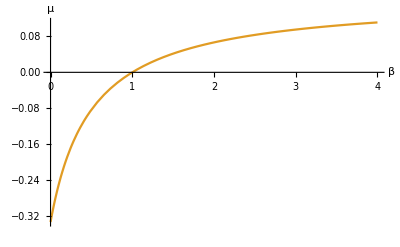

-Graphics3D-

-Graphics3D-

```mathematica
colors=ColorData[97,"ColorList"];
colorsBW={RGBColor[0.3,0.3,0.3],RGBColor[0.6,0.6,0.6],RGBColor[0.9,0.9,0.9]};

fontTicks=18;
fontAxesLabel=22;

p2dColor=Plot[(β-1)/(3(1+2β)),{β,0,4},AxesLabel->{"β","μ"},PlotStyle->colors[[2]]]
p2dBW=Plot[(β-1)/(3(1+2β)),{β,0,4},PlotStyle->colorsBW[[1]]];

Plot3D[{Rsolvneg[μ,β],Rsolvpos[μ,β]},{μ,0,1},{β,0,4},AxesLabel->{"μ","β","R"},PlotRange->{0,2},Mesh->None,TicksStyle->Directive["Label",fontTicks],LabelStyle->Directive[fontAxesLabel]]

Plot3D[{Zsolvneg[μ,β],Zsolvpos[μ,β]},{μ,0,1},{β,0,4},AxesLabel->{"μ","β","Z"},PlotRange->{0,0.25},Mesh->None,TicksStyle->Directive["Label",fontTicks],LabelStyle->Directive[fontAxesLabel]]
```

GreaterEqual::nord: Invalid comparison with 0.0785169-0.214598 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with 0.0785169+0.214598 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with 0.0800106-0.0978956 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

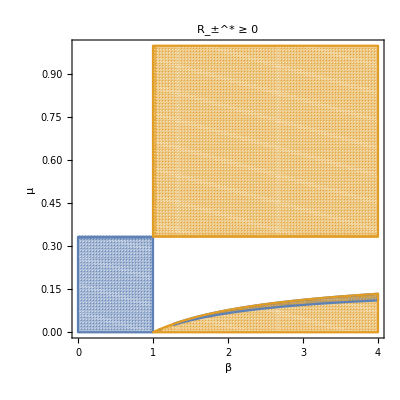

GreaterEqual::nord: Invalid comparison with -0.00612307-0.00797377 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with -0.00612307+0.00797377 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with -0.0176277-0.0225855 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

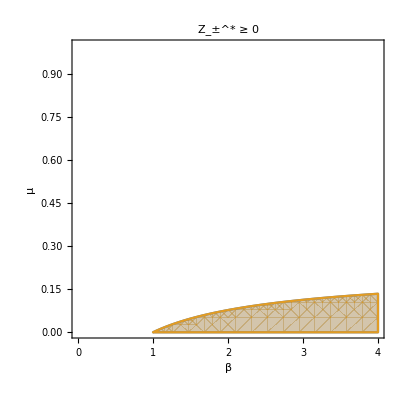

GreaterEqual::nord: Invalid comparison with 0.0133333-0.0832666 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with 0.0133333+0.0832666 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with -0.0377778-0.0416333 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

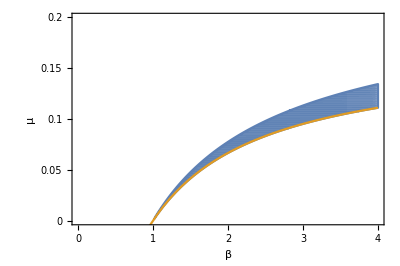

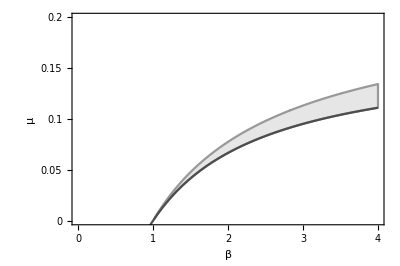

```mathematica
RegionPlot[{Rsolvneg[μ,β]≥0,Rsolvpos[μ,β]≥0},{β,0,4},{μ,0,1},FrameLabel->{"β","μ"},RotateLabel->False,PlotLabel->"R_±^* ≥ 0",FrameTicksStyle->Directive["Label",fontTicks,fontTicks,FontFamily->"Latin Modern Sans"],LabelStyle->Directive[fontAxesLabel,fontTicks,FontFamily->"Latin Modern Math"],PlotPoints->100]
RegionPlot[{Zsolvneg[μ,β]≥0,Zsolvpos[μ,β]≥0},{β,0,4},{μ,0,1},FrameLabel->{"β","μ"},RotateLabel->False,PlotLabel->"Z_±^* ≥ 0",FrameTicksStyle->Directive["Label",fontTicks,fontTicks,FontFamily->"Latin Modern Sans"],LabelStyle->Directive[fontAxesLabel,fontTicks,FontFamily->"Latin Modern Math"]]

rp2dColor=RegionPlot[Rsolvneg[μ,β]≥0&&Rsolvpos[μ,β]≥0&&Zsolvneg[μ,β]≥0&&Zsolvpos[μ,β]≥0,{β,0,4},{μ,0,0.2},PlotRange->{{0,4},{0,0.2}},FrameLabel->{"β","μ"},RotateLabel->False,FrameTicksStyle->Directive["Label",fontTicks,FontFamily->"Latin Modern Sans"],LabelStyle->Directive[fontAxesLabel,FontFamily->"Latin Modern Math"],PlotPoints->300,MeshStyle->Opacity[0],PlotRangePadding->None,FrameStyle->Black,AspectRatio->1/1.5,FrameTicks->{{{0,0.05,0.1,0.15,0.2},None},{{0,1,2,3,4},None}},ImageSize->400];(*PlotLabel->"R_±^* ≥ 0 and Z_±^* ≥ 0",*)

rp2dBW=RegionPlot[Rsolvneg[μ,β]≥0&&Rsolvpos[μ,β]≥0&&Zsolvneg[μ,β]≥0&&Zsolvpos[μ,β]≥0,{β,0,4},{μ,0,0.2},PlotRange->{{0,4},{0,0.2}},FrameLabel->{"β","μ"},RotateLabel->False,FrameTicksStyle->Directive["Label",fontTicks,FontFamily->"Latin Modern Sans"],LabelStyle->Directive[fontAxesLabel,FontFamily->"Latin Modern Math"],PlotStyle->colorsBW[[3]],BoundaryStyle->colorsBW[[2]],PlotPoints->300,MeshStyle->Opacity[0],PlotRangePadding->None,FrameStyle->Black,AspectRatio->1/1.5,FrameTicks->{{{0,0.05,0.1,0.15,0.2},None},{{0,1,2,3,4},None}},ImageSize->400];

plottoexportColor=Show[rp2dColor,p2dColor]
plottoexportBW=Show[rp2dBW,p2dBW]
```

#### Testing values of R_± and Z_± for specific parameter values

```mathematica
βtest=2;
μtest=(βtest-1)/(3(1+2βtest))+0.003;
r1=Rsolvneg[μtest,βtest];
r2=Rsolvpos[μtest,βtest];
z1=Zsolv/.{R->Rsolvneg[μtest,βtest]}/.{μ->μtest,β->βtest};
z2=Zsolv/.{R->Rsolvpos[μtest,βtest]}/.{μ->μtest,β->βtest};

{2 r1 Cos[0]+z1, -r1 Cos[0]-√3 r1 Sin[0]+z1, -r1 Cos[0]+√3 r1 Sin[0]+z1}
{2 r2 Cos[0]+z2, -r2 Cos[0]-√3 r2 Sin[0]+z2, -r2 Cos[0]+√3 r2 Sin[0]+z2}
```

{0.0197136,-0.00957119,-0.00957119}

{0.30162,-0.10354,-0.10354}

```mathematica
r1=0;r2=0;z1=0;z2=0;
{2 r1 Cos[θ]+z1, -r1 Cos[θ]-√3 r1 Sin[θ]+z1, -r1 Cos[θ]+√3 r1 Sin[θ]+z1}
{2 r2 Cos[θ]+z2, -r2 Cos[θ]-√3 r2 Sin[θ]+z2, -r2 Cos[θ]+√3 r2 Sin[θ]+z2}
```

{0,0,0}

{0,0,0}

```mathematica
r1=0.1667;t1=-1.0472;z1=0.11075;
{2 r1 Cos[t1]+z1, -r1 Cos[t1]-√3 r1 Sin[t1]+z1, -r1 Cos[t1]+√3 r1 Sin[t1]+z1}
```

{0.277449,0.277451,-0.22265}

```mathematica
r1=0.14815;t1=0;z1=0.037037;
{2 r1 Cos[t1]+z1, -r1 Cos[t1]-√3 r1 Sin[t1]+z1, -r1 Cos[t1]+√3 r1 Sin[t1]+z1}
```

{0.333337,-0.111113,-0.111113}